```mathematica
Get[NotebookDirectory[]<>#]&/@
{"load_takahashi_data.wl",
"styles.wl"
};
```

## Fit temperature deactivation

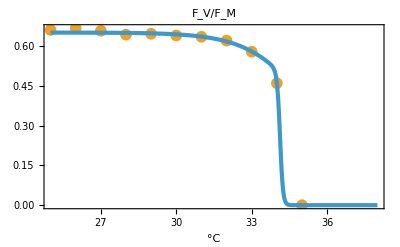

{αPtotalP→9.28571×10^8,αU→5.×10^8,σT1→75880.5,σT2→1.62172×10^6,ρT→0.001,xTref1→0.00175396,xTref2→11271.5,wRef→35.}

```mathematica
FvFmMax=0.65;
fit0={αU->0.5 10^9};
fit1=NSolve[FvFmMax==αPtotalP/(αU+αPtotalP)/.fit0][[1]]~Join~fit0;
αPxxx=αPtotalP ρT/(ρT+xTref1  ⅇ^(-σT1/(w+273))/ⅇ^(-σT1/(wRef+273))+xTref2  ⅇ^(-σT2/(w+273))/ⅇ^(-σT2/(wRef+273)));
FvFmFunc=αPxxx/(αU+αPxxx);

(*FvFmScaling[W_]:=FvFmMax fT[W];*)

FvFmDarkData=Normal[data["FigS1"][Select[#["h"]==0.5&]][All,{#["temp"],#["Fv/Fm"]}&]](*Table[Normal[data["FigS1"][Select[#["h"]==hour&]][All,{#["temp"],#["Fv/Fm"]}&]],{hour,{0.5(*,3.5*)}}]*);
FvFmTempFit=Quiet@NonlinearModelFit[FvFmDarkData, 
{FvFmFunc/.fit1,ρT==10^-3,wRef==35,σT1>0,(*1.4 10^6>*)σT2>0,xTref1>0,xTref2>0},{{σT1,10^5},{σT2,10^6},{ρT,10^-3},{xTref1,10^-3},{xTref2,10^4},{wRef,35}},w];
(Export[NotebookDirectory[]<>"export/direct-temperature-effect/two-step-arrhenius.pdf",#];#)&@Row[{
Show[
ListPlot[FvFmDarkData,
imageSizePadding[ImagePaddingXunits],PlotMarkers->plotMarkers,AxesOrigin->{Automatic},PlotStyle->{{Dashed,colorPoints,thickness}},Joined->False,style],
Plot[FvFmTempFit[W],{W,25,38},Evaluate@style,PlotStyle->{{colorCurves,thickness}}],PlotRange->All,FrameLabel->{{None,None},{w/.units,None}},PlotLabel->"F_V/F_M"]}]
Join[fit1,FvFmTempFit["BestFitParameters"]]
```

## Alternative: single Arrhenius

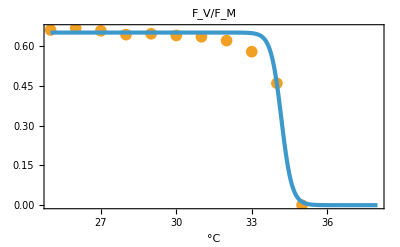

{αPtotalP→9.28571×10^8,αU→5.×10^8,σT→452022.,xTref→0.143918,ρT→0.001,wRef→35.}

```mathematica
FvFmMax=0.65;
fit0={αU->0.5 10^9};
fit1=NSolve[FvFmMax==αPtotalP/(αU+αPtotalP)/.fit0][[1]]~Join~fit0;
αPxxx=αPtotalP ρT/(ρT+xTref  ⅇ^(-σT/(w+273))/ⅇ^(-σT/(wRef+273)));
FvFmFunc=αPxxx/(αU+αPxxx);
FvFmDarkData=Normal[data["FigS1"][Select[#["h"]==0.5&]][All,{#["temp"],#["Fv/Fm"]}&]];
FvFmTempFit=Quiet@NonlinearModelFit[FvFmDarkData, 
{FvFmFunc/.fit1,ρT==10^-3,wRef==35,(*1.4*)(*3 10^5>*)σT>0(*5 10^5*),xTref>0},{{σT,1},{xTref,.01},{ρT,10^-3},{wRef,35}},w];
(Export[NotebookDirectory[]<>"export/direct-temperature-effect/single-step-arrhenius-alternative.pdf",#];#)&@Row[{
Show[
ListPlot[FvFmDarkData,
imageSizePadding[ImagePaddingXunits],PlotMarkers->plotMarkers,AxesOrigin->{Automatic},PlotStyle->{{Dashed,colorPoints,thickness}},Joined->False,style],
Plot[FvFmTempFit[W],{W,25,38},Evaluate@style,PlotStyle->{{colorCurves,thickness}}],PlotRange->All,FrameLabel->{{None,None},{w/.units,None}},PlotLabel->"F_V/F_M"]}]
Join[fit1,FvFmTempFit["BestFitParameters"]]
```